## Dunaev Viktor, 3 kurs, 6 group, 23 variant

## Pre - Task

```mathematica
fname = NotebookDirectory[]<>"input.txt"
```

C:\6_Cemestr\DS_Laguto\input.txt

```mathematica
stream = OpenRead[fname];
```

```mathematica
vertexNum = Read[stream, {Word, Number}]⟦2⟧
```

6

```mathematica
edgesNum =Read[stream, {Word, Number}]⟦2⟧
```

12

```mathematica
edges =Table[#⟦1⟧->#⟦2⟧&[ToExpression[Read[stream]]],edgesNum]
```

{1->5,2->5,3->1,3->4,3->5,4->1,4->2,4->6,5->4,6->2,6->3,6->5}

```mathematica
vertex = Table[i,{i,1,vertexNum}]
```

{1,2,3,4,5,6}

```mathematica
weight = Range[vertexNum]
```

{1,2,3,4,5,6}

```mathematica
Table[(pos = ToExpression[Characters[#⟦1⟧]⟦5⟧];val = #⟦2⟧;weight⟦pos⟧ = val)&[Read[stream, {Word, Number}]],vertexNum]
```

{7,4,-1,-7,-2,-1}

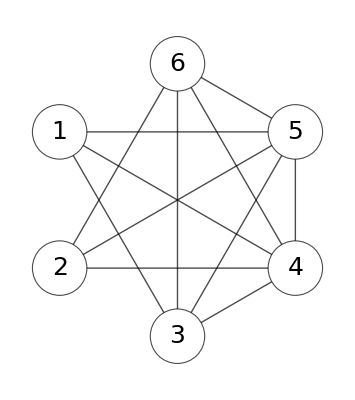

```mathematica
g =Graph[vertex,edges,VertexSize->Large, VertexStyle->White, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,25], GraphLayout->{"CircularEmbedding"},EdgeShapeFunction->"Arrow", EdgeStyle->Black]
```

## Task 1

```mathematica
(* 1) реализовать алгоритм построения частного решения системы уравнений баланса;
 2) найти и вывести частное решение для своей системы уравнений,проверить правильность найденного решения путём подставки решения в систему. *)
```

```mathematica
startNode = RandomChoice[vertex]
```

5

```mathematica
dirs= Table[0,Length[vertex]]
```

{0,0,0,0,0,0}

```mathematica
pred = Table[0, Length[vertex]]
```

{0,0,0,0,0,0}

```mathematica
depth = Table[0 , Length[vertex]]
```

{0,0,0,0,0,0}

```mathematica
dinast = {}
```

{}

```mathematica
tree = {}
```

{}

```mathematica
graphTree = {}
```

{}

```mathematica
DepthFirstScan[UndirectedGraph@g,startNode,{"FrontierEdge"->((edge =#/.(x_<->y_)->(x->y); AppendTo[tree,edge];If[MemberQ[edges,edge],dirs⟦#⟦2⟧⟧=1;AppendTo[graphTree,edge],dirs⟦#⟦2⟧⟧=-1;AppendTo[graphTree,#⟦2⟧->#⟦1⟧]];pred⟦#⟦2⟧⟧=#⟦1⟧;depth⟦#⟦2⟧⟧ = depth⟦#⟦1⟧⟧+1)&)}]
```

{5,4,1,6,5,3}

```mathematica
DepthFirstScan[tree,startNode,{"PrevisitVertex"->((AppendTo[dinast,#])&)}];
```

```mathematica
tree
```

{5->1,1->3,3->6,6->4,4->2}

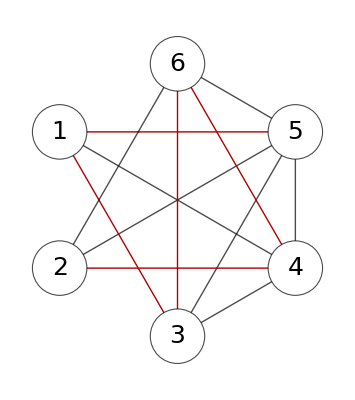

```mathematica
HighlightGraph[g,graphTree]
```

```mathematica
dirs
```

{-1,1,-1,-1,0,-1}

```mathematica
pred
```

{5,4,1,6,0,3}

```mathematica
dinast
```

{5,1,3,6,4,2}

```mathematica
depth
```

{1,5,2,4,0,3}

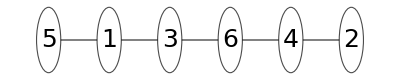

```mathematica
Graph[tree, VertexSize->Large, VertexStyle->White, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,25], GraphLayout->{"RadialEmbedding"},EdgeShapeFunction->"Arrow", EdgeStyle->Black]
```

```mathematica
TableForm[{vertex,pred,depth, dirs},TableHeadings->{{"Вершины","Список предков","Список глубин", "Список направлений"}}]
```

Вершины | 1 | 2 | 3 | 4 | 5 | 6
Список предков | 5 | 4 | 1 | 6 | 0 | 3
Список глубин | 1 | 5 | 2 | 4 | 0 | 3
Список направлений | -1 | 1 | -1 | -1 | 0 | -1

```mathematica
(* Строим частное решение *)
```

```mathematica
(Subscript[z, #⟦1⟧,#⟦2⟧]=0)&/@edges
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
xp = Table[0,Length[vertex] ];
```

```mathematica
For[n = Length[vertex],n>1,n--,
i = dinast⟦n⟧;
xp⟦i⟧+=-dirs⟦i⟧*weight⟦i⟧;
xp⟦pred⟦i⟧⟧+= dirs⟦i⟧*dirs⟦pred⟦i⟧⟧*xp⟦i⟧;
]
```

```mathematica
xp
```

{2,-4,-5,-3,0,-4}

```mathematica
If[dirs⟦#⟧ ==1,Subscript[z, pred⟦#⟧,#]=xp⟦#⟧]&/@Range[vertexNum];
```

```mathematica
If[dirs⟦#⟧ ==-1,Subscript[z, #,pred⟦#⟧]=xp⟦#⟧]&/@Range[vertexNum];
```

```mathematica
pSol = (Subscript[x, #⟦1⟧,#⟦2⟧]->Subscript[z, #⟦1⟧,#⟦2⟧])&/@edges
```

{x_(1,5)→2,x_(2,5)→0,x_(3,1)→-5,x_(3,4)→0,x_(3,5)→0,x_(4,1)→0,x_(4,2)→-4,x_(4,6)→-3,x_(5,4)→0,x_(6,2)→0,x_(6,3)→-4,x_(6,5)→0}

```mathematica
sys=((Total[Join[Select[edges,MatchQ[#->_]],-Select[edges,MatchQ[_->#]]]]& /@vertex/.(a_->b_)->Subscript[x, a,b])⟦#⟧==weight⟦#⟧)&/@vertex
```

{x_(1,5)-x_(3,1)-x_(4,1)==7,x_(2,5)-x_(4,2)-x_(6,2)==4,x_(3,1)+x_(3,4)+x_(3,5)-x_(6,3)==-1,-x_(3,4)+x_(4,1)+x_(4,2)+x_(4,6)-x_(5,4)==-7,-x_(1,5)-x_(2,5)-x_(3,5)+x_(5,4)-x_(6,5)==-2,-x_(4,6)+x_(6,2)+x_(6,3)+x_(6,5)==-1}

```mathematica
(* проверка *)
```

```mathematica
sys/.pSol
```

{True,True,True,True,True,True}